# Start with simple networks to understand the constituents

## Layers

### Basic Layers

### LinearLayer

The LinearLayer is a standard layer that connects to neurons of the previous layer with the corresponding weight an bias according to w*v+b

```mathematica
trained=NetTrain[LinearLayer[],{1->1.9,2->4.1,3->6.0,4->8.1}]
```

LinearLayer[<>]

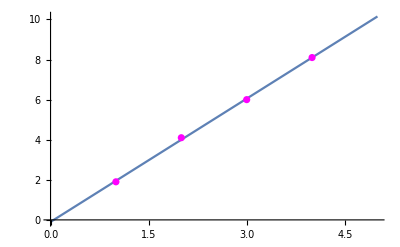

```mathematica
Show[Plot[trained[x],{x,0,5}],
ListPlot[{{1,1.9},{2,4.1},{3,6.0},{4,8.1}},PlotStyle->Magenta]]
```

The action of the LinearLayer can be simulated by the following function

```mathematica
linear[data_, weight_,bias_]:=Dot[weight,data]+bias
```

```mathematica
layer =NetInitialize@LinearLayer[2,"Input"->3]
```

LinearLayer[<>]

```mathematica
weights=NetExtract[layer,"Weights"]
biases=NetExtract[layer,"Biases"]
```

{{0.138344,-0.166716,0.481384},{-0.779705,0.563995,0.335758}}

{0.,0.}

```mathematica
inData={1.,2.,3.}
```

{1.,2.,3.}

```mathematica
linear[inData,weights,biases]
layer[inData]
```

{1.24906,1.35556}

{1.24906,1.35556}

### SoftmaxLayer

The SoftmaxLayer just normalizes all ingredients to allow for an interpretation in terms of probabilities.
The exponential function is applied to all entries of the layer to guarantee that all values are greater than zero and finally they are normalized by the overall sum

```mathematica
softmax=SoftmaxLayer[]
```

SoftmaxLayer[<>]

```mathematica
v={1.,-1.,3.,4.,5.,14.}
```

{1.,-1.,3.,4.,5.,14.}

```mathematica
softmax[v]
```

{2.2599×10^-6,3.05845×10^-7,0.0000166986,0.0000453914,0.000123387,0.999812}

```mathematica
Normalize[Exp[v],Total]
```

{2.2599×10^-6,3.05845×10^-7,0.0000166986,0.0000453914,0.000123387,0.999812}

#### ElementwiseLayer

The ElementwiseLayer applies a unary function f to every element of the input data. The example shows a hard sigmoid function. The # is a placeholder for the first argument provided and the & indicates, that a pure function is defined.

```mathematica
hsig = Clip[(#+1)/2,{0,1}]&
hsigLayer=ElementwiseLayer[hsig,"Input"->"Real"]
```

Clip[(#1+1)/2,{0,1}]&

ElementwiseLayer[<>]

{-1,0,0.5,1,1.5}

{0,1/2,0.75,1,1}

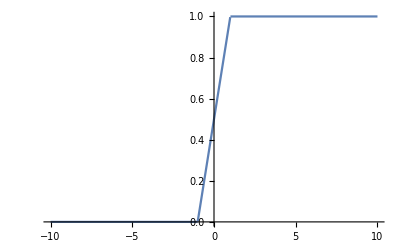

```mathematica
data = {-1,0,0.5,1,1.5}
hsig[data]
Plot[hsig[x],{x,-10,10}]
```

The second function shows a Tanh function applied to the data

1/2 (Tanh[#1]+1)&

ElementwiseLayer[<>]

{0.119203,0.5,0.731059,0.880797,0.952574}

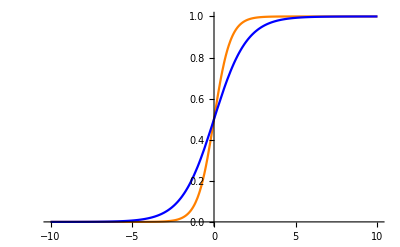

```mathematica
tanh = (Tanh[#]+1)/2&
tanhLayer=ElementwiseLayer[tanh,"Input"->"Real"]
tanhLayer[data]
Show[Plot[tanh[x],{x,-10,10},PlotStyle->Orange],Plot[LogisticSigmoid[x],{x,-10,10},PlotStyle->Blue]]
```

### Loss Layers

#### CrossEntropyLossLayer

Here is the function computed by CrossEntropyLossLayerpaclet:ref/CrossEntropyLossLayer["Binary"]:

```mathematica
bceLoss=-(#Target*Log[#Input]+(1-#Target)*Log[1-#Input])&
```

-(#Target Log[#Input]+(1-#Target) Log[1-#Input])&

```mathematica
input={0.2,0.3,0.4,0.5}
output = {0.1,0.2,0.3,0.4}
Map[(#+0.1)&,output]
bceLoss[<|"Input"->input,"Target"->input|>]
```

{0.2,0.3,0.4,0.5}

{0.1,0.2,0.3,0.4}

{0.2,0.3,0.4,0.5}

{0.500402,0.610864,0.673012,0.693147}

```mathematica
bceLoss[<|"Input"->0.00001,"Target"->0.00001|>]
```

0.000125129

When the target is fixed at 1 or 0, the loss is minimized as the input approaches 1 or 0:

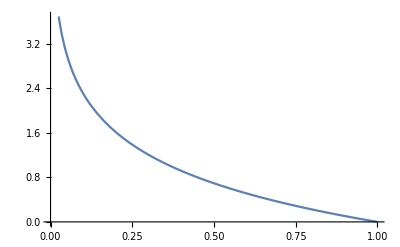

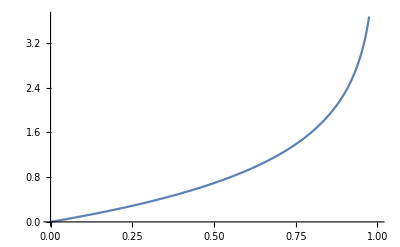

```mathematica
Plot[Evaluate@bceLoss[<|"Input"->p,"Target"->1|>],{p,0,1}]
Plot[Evaluate@bceLoss[<|"Input"->p,"Target"->0|>],{p,0,1}]
```

In general, the loss is minimized when the target approaches the input:

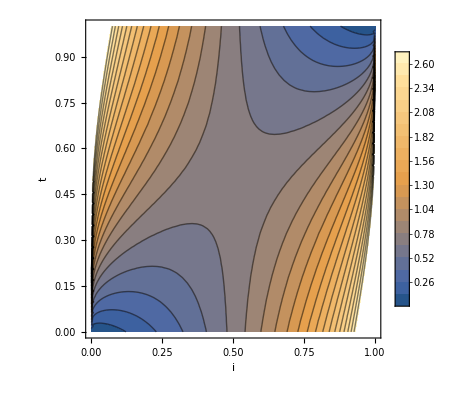

```mathematica
ContourPlot[Evaluate@bceLoss[<|"Input"->i,"Target"->t|>],{i,0,1},{t,0,1},Contours->20,PlotLegends->Automatic,PlotRangePadding->0,FrameLabel->Automatic]
```

1. CrossEntropyLayer[“Binary”] is used automatically by NetTrainpaclet:ref/NetTrain when the final activation used for an output is an ElementwiseLayerpaclet:ref/ElementwiseLayer[LogisticSigmoidpaclet:ref/LogisticSigmoid]. 
2. CrossEntropyLossLayerpaclet:ref/CrossEntropyLossLayer["Index"] is used automatically by NetTrainpaclet:ref/NetTrain when the final activation used for an output is a SoftmaxLayerpaclet:ref/SoftmaxLayer.

Ad 1.) Create a network that takes a pair of numbers and produces either Truepaclet:ref/True or Falsepaclet:ref/False:

```mathematica
net=NetChain[{LinearLayer[],LogisticSigmoid},"Input"->2,"Output"->"Boolean"]
```

NetChain[<>]

```mathematica
data = Flatten@Table[{i,j}->(i>j),{i,5},{j,5}]
```

{{1,1}→False,{1,2}→False,{1,3}→False,{1,4}→False,{1,5}→False,{2,1}→True,{2,2}→False,{2,3}→False,{2,4}→False,{2,5}→False,{3,1}→True,{3,2}→True,{3,3}→False,{3,4}→False,{3,5}→False,{4,1}→True,{4,2}→True,{4,3}→True,{4,4}→False,{4,5}→False,{5,1}→True,{5,2}→True,{5,3}→True,{5,4}→True,{5,5}→False}

```mathematica
results=NetTrain[net,data,All]
```

NetTrainResultsObject[<>]

```mathematica
results["TrainingNet"]
```

NetGraph[<>]

```mathematica
results["TrainingNet"][["LossNet1"]]
```

CrossEntropyLossLayer[<>]

```mathematica
trained = results["TrainedNet"]
```

NetChain[<>]

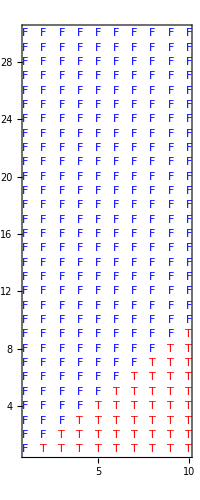

```mathematica
Graphics[Table[Text[If[trained[{i,j}],Style["T",Red],Style["F",Blue]],{i,j}],{i,30},{j,30}],Frame->True]
```

```mathematica
Plot3D[trained[{x,y},None],{x,0,10},{y,0,10},NormalsFunction->Automatic,ImagePadding->{{20,5},{0,0}}]
```

-Graphics3D-

Ad 2.) CrossEntropyLossLayerpaclet:ref/CrossEntropyLossLayer["Index"] is used automatically by NetTrainpaclet:ref/NetTrain when the final activation used for an output is a SoftmaxLayerpaclet:ref/SoftmaxLayer. Create an artificial dataset from three normally distributed clusters:

```mathematica
makeCluster[class_,μ_,ρ_]:=RandomVariate[MultinormalDistribution[μ,{{1,2ρ},{2ρ,4}}],60000]->class;
```

```mathematica
clusters=makeCluster@@@{{Red,{1.5,1.5},-.2},{Green,{-1.5,1},.1},{Blue,{0,-2.5},.8}}
```

{{{2.56045,0.0999637},{1.19033,0.72028},{1.75055,3.0877},{0.416668,0.912874},59993,{1.77451,1.28027},{0.763144,-0.488583},{3.31622,1.61207}}→RGBColor[1, 0, 0],{1}→RGBColor[0, 1, 0],{1}→RGBColor[0, 0, 1]}
 |  |  |  |

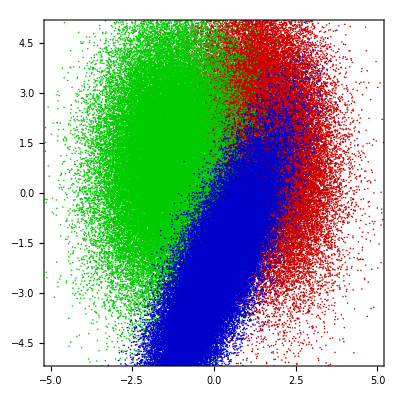

```mathematica
plot=ListPlot[Keys[clusters], PlotStyle->{RGBColor[0.8, 0., 0.],RGBColor[0., 0.8, 0.],RGBColor[0., 0., 0.8]},AspectRatio->1,Frame->True,PlotRange->{{-5,5},{-5,5}}]
```

```mathematica
trainingData=Flatten[Thread/@clusters];
RandomSample[trainingData,6]
```

{{2.05439,2.8383}→RGBColor[0, 0, 1],{2.23781,-0.743332}→RGBColor[1, 0, 0],{-1.29842,4.21338}→RGBColor[0, 1, 0],{-0.0812182,-2.98379}→RGBColor[0, 0, 1],{2.69744,1.12449}→RGBColor[1, 0, 0],{-1.61471,0.176246}→RGBColor[0, 1, 0]}

Create a net to compute the probability of a point lying in each cluster, using a "Class" decoder to classify the input as either Redpaclet:ref/Red, Greenpaclet:ref/Green or Bluepaclet:ref/Blue:

```mathematica
net=NetChain[{30,Ramp,3,SoftmaxLayer[]},"Input"->{2},"Output"->NetDecoder[{"Class",{Red,Green,Blue}}]]
```

NetChain[<>]

```mathematica
results=NetTrain[net,trainingData,All]
```

NetTrainResultsObject[<>]

```mathematica
results["TrainingNet"][["LossNet1"]]
```

CrossEntropyLossLayer[<>]

```mathematica
trained=results["TrainedNet"]
```

NetChain[<>]

```mathematica
trained[{{1.5,1},{-1.5,1},{0,-3}}]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

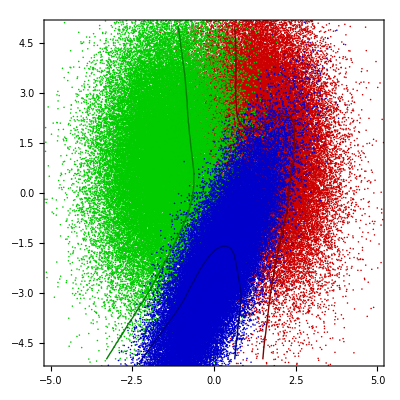

```mathematica
Show[plot,Quiet@Table[ContourPlot[trained[{x,y},{"Probability",color}]==0.9,{x,-5,5},{y,-5,5},ContourStyle->{Thick,Darker[color,.5]}],{color,{Red,Green,Blue}}]]
```

## Activation Functions

### LogisticSigmoid

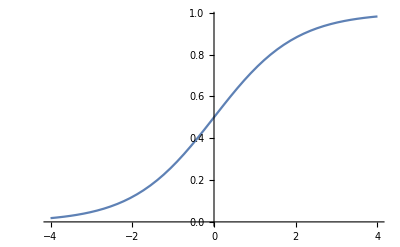

```mathematica
Plot[LogisticSigmoid[x],{x,-4,4}]
```

### Ramp

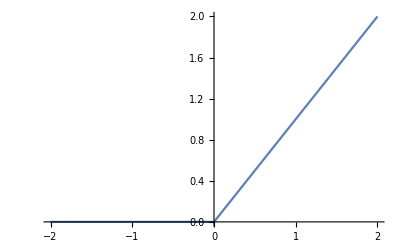

```mathematica
Plot[Ramp[x], {x,-2,2}]
```

### Tanh

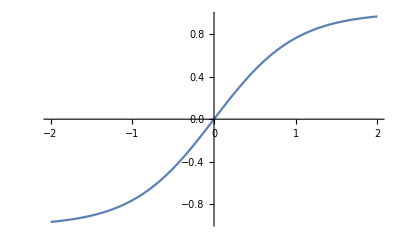

```mathematica
Plot[Tanh[x], {x,-2,2}]
```